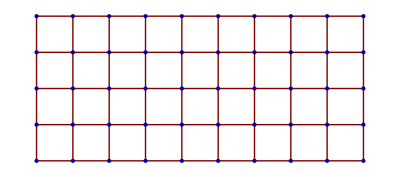

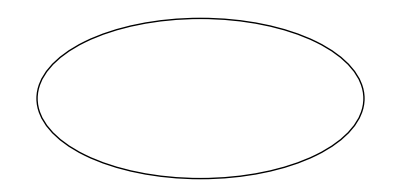

-Graphics-L r x L

{{0,0},{0,1},{1,1},{1,0},{0,0},{1,1}}

```mathematica
a=GraphPlot[GridGraph[{5,10}], PlotStyle->PointSize[Large],PlotRangePadding->None]
b=Graphics[{Thick,Circle[{5.5,3},{2.87228,1.414}]}]
a=Labeled[Show[a],{Style["L ",20],Style["r x L",20]},{Bottom,Left},RotateLabel->True]
```

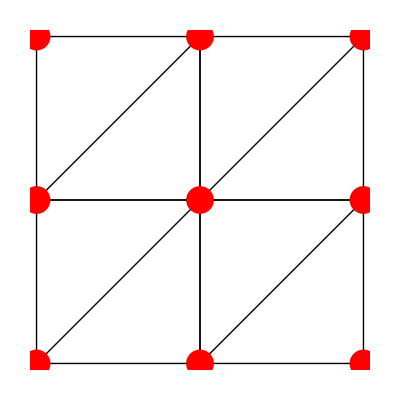

```mathematica
data={{0,0},{0,1},{1,1},{1,0},{0,0},{1,1}};
a=Graphics[{Thick,Line[data], Line[Map[#+{0,1}&,data]],Line[Map[#+{1,0}&,data]],Line[Map[#+{1,1}&,data]]}];
b=Graphics[{PointSize[0.05],Red,Point[Flatten[Table[{x,y},{x,0,2},{y,0,2}],1]]}];
SetDirectory[NotebookDirectory[]];
SetDirectory["Images"];
Export["TriLattice.png",Show[a,b]];
Show[a,b]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb\Images

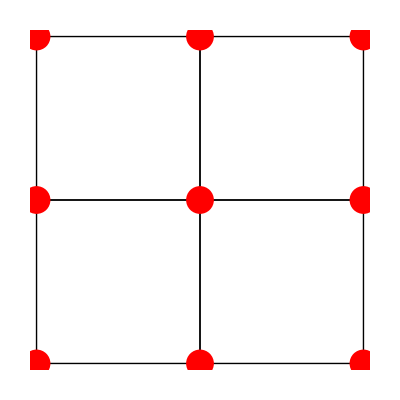

```mathematica
data={{0,0},{0,1},{1,1},{1,0},{0,0}};
a=Graphics[{Thick,Line[data], Line[Map[#+{0,1}&,data]],Line[Map[#+{1,0}&,data]],Line[Map[#+{1,1}&,data]]}];
b=Graphics[{PointSize[0.05],Red,Point[Flatten[Table[{x,y},{x,0,2},{y,0,2}],1]]}];
SetDirectory[NotebookDirectory[]]
SetDirectory["Images"]
Export["SqLattice.png",Show[a,b]];
Show[a,b]
```